```mathematica
Exit
```

```mathematica
(*UninstallPackages[$PM,"RepulsorLink"];*)
```

```mathematica
Needs["PM`"]
LoadPackages[{"Geometries","RepulsorLink"}];
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"SOCSLink.m"}]]
```

WARNING: LTemplate has not yet been tested with Mathematica 13.2.1.
The latest supported Mathematica version is 12.3.1.
Please report any issues you find to szhorvat at gmail.com.

$packageDirectory→/Users/Henrik/github/SOCSLink/

$libraryDirectory→/Users/Henrik/github/SOCSLink/LibraryResources/MacOSX-ARM64

$sourceDirectory→/Users/Henrik/github/SOCSLink/LibraryResources/Source

This is the package SOCSLink` installed at:

/Users/Henrik/github/SOCSLink/

$buildSettings→{CompileOptions→{ -Wall,-Wextra,-Wno-unused-parameter,-mmacosx-version-min=13.5.2,-std=c++20,-mcpu=native -mtune=native,-ffast-math,-fno-math-errno,-Ofast,-flto,-pthread,-gline-tables-only,-gcolumn-info,-framework Accelerate},LinkerOptions→{-lm,-ldl},IncludeDirectories→{/Users/Henrik/github/SOCSLink/LibraryResources/Source},LibraryDirectories→{},ShellOutputFunction→Print}

```mathematica
M=SphereMesh[4];
A=WeakLaplacian[M]+Mass[M];
```

```mathematica
M=SpotSurface[4];
A=WeakLaplacian[M]+Mass[M];
```

/Users/Henrik/Library/CloudStorage/Dropbox/Mathematica/PackageSources/Mesh/Geometries/Spot

```mathematica
ClearAllCache[M];
(*perm=SparseArray`NestedDissection[A]-1;//AbsoluteTiming*)
R=Make["RepulsorObject"];
ClearProfile[R];
R=Repulsor[M];//AbsoluteTiming
T=ClusterCount[R];//AbsoluteTiming
perm=NestedDissectionOrdering[R];//AbsoluteTiming
p=ImportProfile["Tools_Profile.tsv"];//AbsoluteTiming
```

Profile will be written to /Users/Henrik/Tools_Profile.tsv.

Log     will be written to /Users/Henrik/Tools_Log.txt.

{0.010645,Null}

{0.37907,Null}

{0.1732,Null}

{0.095296,Null}

```mathematica
ClusterCount[R]
```

```mathematica
LeafClusterCount[R]
```

910396

```mathematica
Sunburst[p,41]
```

```mathematica
Sunburst[p]
```

-Graphics-

```mathematica
S=Make["SOCS"];
S["Init"[A["RowPointers"],A["ColumnIndices"]-1,A["NonzeroValues"],perm,ThreadCount[]]];//AbsoluteTiming
S["Refactorize"[A["NonzeroValues"]]];//AbsoluteTiming
```

thread_count = 8

{0.711074,Null}

thread_count = 8

{0.490143,Null}

```mathematica
STrue=LinearSolve[A];//AbsoluteTiming
```

```mathematica
STrue=LinearSolve[A,Method->"Cholesky"];//AbsoluteTiming
```

{3.46835,Null}

```mathematica
xTrue=RandomReal[{-1,1},Length[A]];
b=A.xTrue;
x=S["SolveVector"[b]];//AbsoluteTiming
Max[Abs[x-xTrue]]

STrue[b];//AbsoluteTiming
```

{0.065746,Null}

1.53266×10^-13

{0.101661,Null}

```mathematica
XTrue=RandomReal[{-1,1},{Length[A],8}];
B=A.XTrue;
X=S["SolveMatrix"[B]];//AbsoluteTiming
Max[Abs[X-XTrue]]

STrue[B];//AbsoluteTiming
```

{0.157559,Null}

3.25406×10^-13

{0.815832,Null}

```mathematica
$libraryDirectory="/Users/Henrik/github/SOCSLink/LibraryResources/MacOSX-ARM64";

Quiet[LibraryFunctionUnload/@DownValues[cNestedDissectionOrderingFEM][[1;;-2,2]]];
ClearAll[cNestedDissectionOrderingFEM];
cNestedDissectionOrderingFEM[PointCount_Integer?Positive,AmbDim_Integer?Positive]:=Module[{lib, libname, code, name, t},

	name = "cNestedDissectionOrderingFEM";

	libname = name<>"_"<>IntegerString[PointCount]<>"_"<>IntegerString[AmbDim];
	
	lib = FileNameJoin[{$libraryDirectory, libname<>CCompilerDriver`CCompilerDriverBase`$PlatformDLLExtension}];
	
	Print[lib];
	
	If[True(*Not[FileExistsQ[lib]]*),

		Print["Compiling "<>libname<>"..."];

		code = StringJoin["

#define NDEBUG
//#define TOOLS_DEBUG
#define TOOLS_ENABLE_PROFILER


#include \"WolframLibrary.h\"
#include \"Repulsor/MMA.h\"

#define LAPACK_DISABLE_NAN_CHECK
#define ACCELERATE_NEW_LAPACK
#include <Accelerate/Accelerate.h>

#include \"NestedDissectionOrdering_FEM.hpp\"

using Real = mreal;
using Int  = mint;

constexpr static Int POINT_COUNT = "<>IntegerString[PointCount]<>";
constexpr static Int AMB_DIM     = "<>IntegerString[AmbDim]<>";

EXTERN_C DLLEXPORT int "<>libname<>"(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
	Profiler::Clear(\""<>$HomeDirectory<>"\");

	MTensor vertex_coords = MArgument_getMTensor(Args[0]);
	MTensor elements      = MArgument_getMTensor(Args[1]);

	const Int split_threshold    = int_cast<Int>(MArgument_getInteger(Args[2]));
	const Int max_level          = int_cast<Int>(MArgument_getInteger(Args[3]));
	const Int thread_count       = int_cast<Int>(MArgument_getInteger(Args[4]));
	const Int local_thread_count = int_cast<Int>(MArgument_getInteger(Args[5]));

	const Int vertex_count  = libData->MTensor_getDimensions(vertex_coords)[0];
	const Int element_count = libData->MTensor_getDimensions(elements)[0];
	
	MTensor perm;

	(void)libData->MTensor_new( MType_Integer, 1, &vertex_count, &perm);

	NestedDissectionOrdering_FEM<POINT_COUNT,AMB_DIM,Real,Int>(
		libData->MTensor_getRealData(vertex_coords), vertex_count,
		libData->MTensor_getIntegerData(elements),   element_count,         
		libData->MTensor_getIntegerData(perm),
		split_threshold,
		max_level,
		thread_count,
		local_thread_count
	);

	MArgument_setMTensor(Res, perm);

	return LIBRARY_NO_ERROR;
}"];

		(* Invoke CreateLibrary to compile the C++ code. *)
		t = AbsoluteTiming[
			lib=CreateLibrary[
				code,
				libname,
				"Language"->"C++",
				"TargetDirectory"-> $libraryDirectory,
				(*"ShellCommandFunction"->Print,*)
				"ShellOutputFunction"->Print,
				Get["/Users/Henrik/github/SOCSLink/BuildSettings.m"]
			]
		][[1]];
		Print["Compilation done. Time elapsed = ", t, " s.\n"];
	];

	cNestedDissectionOrderingFEM[PointCount,AmbDim] = LibraryFunctionLoad[lib,libname,
		{
			{Real,2,"Constant"},
			{Integer,2,"Constant"},
			Integer,Integer, Integer, Integer
		},
		{Integer,1}
	]
];
```

```mathematica
T1=AbsoluteTiming[
perm1=cNestedDissectionOrderingFEM[3,3][VertexCoordinates[M],Simplices[M]-1,
16 2,64,ThreadCount[],ThreadCount[]];
][[1]]
prof=ImportProfile["Tools_Profile.tsv"];
Sunburst[prof]

S=Make["SOCS"];
T2=AbsoluteTiming[
S["Init"[A["RowPointers"],A["ColumnIndices"]-1,A["NonzeroValues"],perm1,ThreadCount[]]];
][[1]]

T1+T2
```

Profile will be written to /Users/Henrik/Tools_Profile.tsv.

Log     will be written to /Users/Henrik/Tools_Log.txt.

0.277021

-Graphics-

thread_count = 8

0.62708

0.904101

```mathematica
perm[[1;;100]]
```

{108988,31897,378764,172443,734616,378768,378769,378765,654900,156677,156679,336778,336790,718853,718854,718857,460852,336789,654892,156687,654893,654904,24901,156686,336792,336793,108986,378766,378767,654890,654899,654894,378786,378784,536896,31900,378782,108989,378783,378785,654901,156747,336913,718927,336898,336900,336910,718914,156737,718913,24921,336912,108987,156739,156746,336909,654896,654897,718917,460866,748300,655141,460865,718944,718945,460863,45580,186124,460867,249535,654903,460854,186122,654905,45579,108991,460856,460860,654907,186123,460855,460857,460861,655139,748298,748299,249531,249533,460858,460859,654895,654906,10358,45578,108990,249530,249532,249534,378787,460850}

```mathematica
perm1[[1;;100]]
```

{127185,277799,478545,478547,478549,572,50204,50205,190748,190749,277793,277796,277801,689363,689364,50203,478544,15068,15069,127187,127189,190746,190747,277790,277795,277797,277798,277800,478539,478542,478546,478548,581579,689365,84542,84551,225092,277778,277781,277786,423452,423457,581559,581560,581576,581585,689357,689362,39345,50202,84548,127179,127182,127188,277784,277787,277791,277792,277794,423453,423454,423455,478538,478540,478541,478543,581561,581570,581577,581578,581588,689360,689361,39342,277779,423419,423464,581592,6284,39339,84530,84536,84539,84544,84547,84552,84553,127180,127183,179893,225088,225090,225091,225093,225096,423417,423418,423434,423438,423439}

-Graphics-

thread_count = 8

0.61893

0.953927

```mathematica
xTrue=RandomReal[{-1,1},Length[A]];
b=A.xTrue;
x=S["SolveVector"[b]];//AbsoluteTiming
Max[Abs[x-xTrue]]

STrue[b];//AbsoluteTiming
XTrue=RandomReal[{-1,1},{Length[A],8}];
B=A.XTrue;
X=S["SolveMatrix"[B]];//AbsoluteTiming
Max[Abs[X-XTrue]]

STrue[B];//AbsoluteTiming
```

{0.068181,Null}

2.83329×10^-13

{0.,Null}

{0.163773,Null}

3.33289×10^-13

-Graphics-

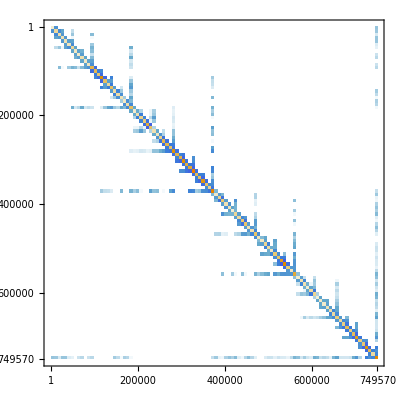

```mathematica
p=perm1+1;
A[[p,p]]//MatrixPlot
```

-Graphics-

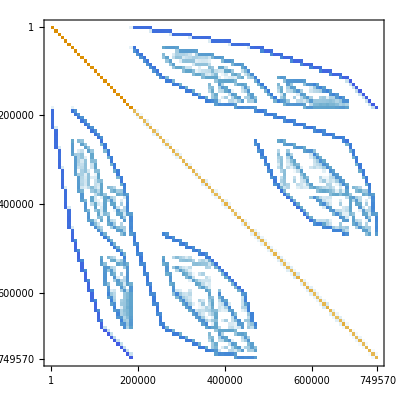

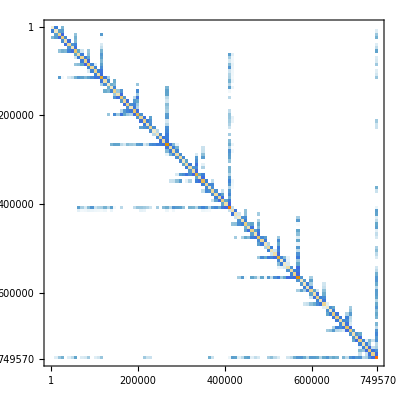

```mathematica
Sunburst[prof]
```

```mathematica
p==Range[Length[p]]
```

True